# Plateau - fixed point solution - generic K and M

```mathematica
Clear[Q,CC,R,S,r,M]
```

```mathematica
(*Define functions based on the given equations*)
J2[mat_]:=(2/Pi)*(1+mat[[1,1]]+mat[[2,2]]+mat[[1,1]] mat[[2,2]]-mat[[1,2]]^2)^(-1/2)
I3[mat_]:=(2/Pi)*(1/Sqrt[Λ3[mat]])*(mat[[2,3]] (1+mat[[1,1]])-mat[[1,2]] mat[[1,3]])/(1+mat[[1,1]])

I4[mat_]:=(4/Pi^2)*(1/Sqrt[Λ4[mat]])*ArcSin[Λ0[mat]/Sqrt[Λ1[mat] Λ2[mat]]]

(*Define auxiliary functions*)

Λ4[mat_]:=(1+mat[[1,1]]) (1+mat[[2,2]])-mat[[1,2]]^2

Λ3[mat_]:=(1+mat[[1,1]]) (1+mat[[3,3]])-mat[[1,3]]^2

Λ0[mat_]:=Λ4[mat] mat[[3,4]]-mat[[2,3]] mat[[2,4]] (1+mat[[1,1]])-mat[[1,3]] mat[[1,4]] (1+mat[[2,2]])+mat[[1,2]] mat[[1,3]] mat[[2,4]]+mat[[1,2]] mat[[1,4]] mat[[2,3]]

Λ1[mat_]:=Λ4[mat] (1+mat[[3,3]])-mat[[2,3]]^2 (1+mat[[1,1]])-mat[[1,3]]^2 (1+mat[[2,2]])+2 mat[[1,2]] mat[[1,3]] mat[[2,3]]

Λ2[mat_]:=Λ4[mat] (1+mat[[4,4]])-mat[[2,4]]^2 (1+mat[[1,1]])-mat[[1,4]]^2 (1+mat[[2,2]])+2 mat[[1,2]] mat[[1,4]] mat[[2,4]]
```

```mathematica
α=√(1/(-MM+(1+(-1+KK) r)^2+√(MM^2+(-1+KK) r (1+(-1+KK) r)^2 (2+(-1+KK) r))))/.{KK->M,MM->M};
```

```mathematica
Q0=M α^2;
C0=M α^2;
R0=α;
S0=α;
```

```mathematica
eqdR=r(I3[{{Q,R,S},{R,1,0},{S,0,1}}](M-1)+I3[{{Q,R,R},{R,1,1},{R,1,1}}])-r(I3[{{Q,R,Q},{R,1,R},{Q,R,Q}}]+r(M-1)I3[{{Q,R,CC},{R,1,S},{CC,S,Q}}])/.{Q->Q0+ϵ Q1,CC->C0+ϵ C1,R->R0+ϵ R1,S->S0+ϵ S1};
```

```mathematica
eqdS=r(I3[{{Q,S,S},{S,1,0},{S,0,1}}](M-2)+I3[{{Q,S,R},{S,1,0},{R,0,1}}]+I3[{{Q,S,S},{S,1,1},{S,1,1}}])-r(I3[{{Q,S,Q},{S,1,S},{Q,S,Q}}]+r I3[{{Q,S,CC},{S,1,R},{CC,R,Q}}]+r(M-2)I3[{{Q,S,CC},{S,1,S},{CC,S,Q}}])/.{Q->Q0+ϵ Q1,CC->C0+ϵ C1,R->R0+ϵ R1,S->S0+ϵ S1};
```

```mathematica
eqdQ=2r I3[{{Q,Q,R},{Q,Q,R},{R,R,1}}] +2 r (M-1)I3[{{Q,Q,S},{Q,Q,S},{S,S,1}}]-2r I3[{{Q,Q,Q},{Q,Q,Q},{Q,Q,Q}}]-2 r^2(M-2)I3[{{Q,Q,CC},{Q,Q,CC},{Q,Q,CC}}]/.{Q->Q0+ϵ Q1,CC->C0+ϵ C1,R->R0+ϵ R1,S->S0+ϵ S1};
```

```mathematica
eqdC=2r I3[{{Q,CC,R},{CC,Q,S},{R,S,1}}]+2r I3[{{Q,CC,S},{CC,Q,R},{S,R,1}}]+2r (M-2)I3[{{Q,CC,S},{CC,Q,S},{S,S,1}}]-r(r+1)I3[{{Q,CC,Q},{CC,Q,CC},{Q,CC,Q}}]-r(r+1)I3[{{Q,CC,CC},{CC,Q,Q},{CC,Q,Q}}]-2r^2(M-2)I3[{{Q,CC,CC},{CC,Q,CC},{CC,CC,Q}}]/.{Q->Q0+ϵ Q1,CC->C0+ϵ C1,R->R0+ϵ R1,S->S0+ϵ S1};
```

```mathematica
eqdRExp=Coefficient[Series[eqdR,{ϵ,0,1}],ϵ,1];
```

```mathematica
eqdSExp=Coefficient[Series[eqdS,{ϵ,0,1}],ϵ,1];
```

```mathematica
eqdQExp=Coefficient[Series[eqdQ,{ϵ,0,1}],ϵ,1];
```

```mathematica
eqdCExp=Coefficient[Series[eqdC,{ϵ,0,1}],ϵ,1];
```

```mathematica
a11=Coefficient[eqdRExp,R1,1];
```

```mathematica
a12=Coefficient[eqdRExp,S1,1];
```

```mathematica
a13=Coefficient[eqdRExp,Q1,1];
```

```mathematica
a14=Coefficient[eqdRExp,C1,1];
```

```mathematica
a21=Coefficient[eqdSExp,R1,1];
a22=Coefficient[eqdSExp,S1,1];
a23=Coefficient[eqdSExp,Q1,1];
a24=Coefficient[eqdSExp,C1,1];
```

```mathematica
a31=Coefficient[eqdQExp,R1,1];
a32=Coefficient[eqdQExp,S1,1];
a33=Coefficient[eqdQExp,Q1,1];
a34=Coefficient[eqdQExp,C1,1];
```

```mathematica
a41=Coefficient[eqdCExp,R1,1];
a42=Coefficient[eqdCExp,S1,1];
a43=Coefficient[eqdCExp,Q1,1];
a44=Coefficient[eqdCExp,C1,1];
```

```mathematica
AA[M_,r_]={{a11,a12,a13,a14},{a21,a22,a23,a24},{a31,a32,a33,a34},{a41,a42,a43,a44}};
```

```mathematica
unstableEig[M_,r_]:=Max[Re[Eigenvalues[AA[M,r]]]];
```

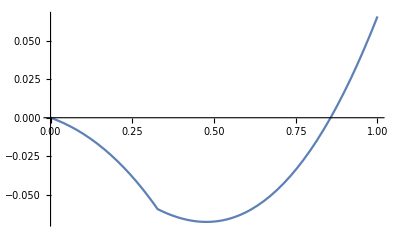

```mathematica
Plot[unstableEig[2,r],{r,0,1}]
```

```mathematica
Table[FindRoot[unstableEig[M,r]==0,{r,1,0.1,1}],{M,2,10}]
```

```mathematica
Monitor[Table[r/. FindRoot[unstableEig[M,r]==0,{r,1,0.1,1}],{M,2,10}],ProgressIndicator[M,{2,10}]]
```

{0.856594,0.908781,0.93317,0.947275,0.956464,0.962925,0.967716,0.97141,0.974345}

```mathematica
Monitor[Table[r/. FindRoot[unstableEig[M,r]==0,{r,1,0.1,1}],{M,11,20}],ProgressIndicator[M,{11,20}]]
```

{0.976734,0.978715,0.980386,0.981813,0.983047,0.984123,0.985072,0.985913,0.986665,0.98734}